Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

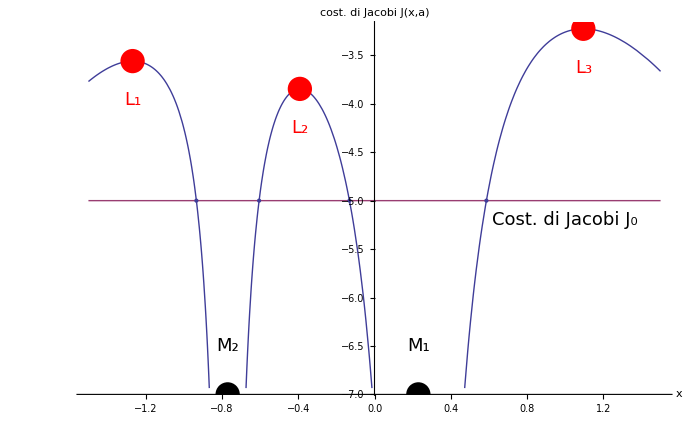

```mathematica
(*
   * Author: Panichi Federico
* Unit Name:Jacobi2dSection
   * Unit Type: program.nb
   * Project: Master Thesis
   * Package: none
   * Language: Mathematica 9.0
   * Description: Calculate the Jacobi constant and the Jacobi surface (J) that is equal to J=2U, where U is the potential wall of the restricted three body problem
   * Invocation: none
*)


a=0.23;
J=-5;
U[x_,y_,a_]:=-((1-a)/Sqrt[(x-a)^2+y^2])-a/Sqrt[(x+1-a)^2+y^2]- 0.5*(x^2+y^2);

f[x_] := 2*U[x, 0, a];
g[x_] := J;
{max1,val1} = Maximize[{2*U[x,0,a], x < a-1}, x];

{max2,val2} = Maximize[{2*U[x,0,a], a-1 < x < a}, x];

{max3,val3} = Maximize[{2*U[x,0,a], x > a}, x];

sol = x /. NSolve[g[x] == f[x] && -1.5 < x < 1.5, x];
t=Show[
	Plot[{f[x], g[x]}, {x, -1.5, 1.5},AxesLabel->{Style["x",Italic,20],Style["cost. di Jacobi J(x,a)",Italic,20]},
		Epilog -> { 
			{Red, PointSize[0.025], 
			Point[{x /. val1, max1}], 
			Point[{x /. val2, max2}],
			Point[{x /. val3, max3}],
			Text[Style["\!\(\*SubscriptBox[\(L\), \(1\)]\)",Italic,18],{x /. val1, max1-0.4}],
			Text[Style["\!\(\*SubscriptBox[\(L\), \(2\)]\)",Italic,18],{x /. val2, max2-0.4}],
			Text[Style["\!\(\*SubscriptBox[\(L\), \(3\)]\)",Italic,18],{x /. val3, max3-0.4}]},
			{Black, PointSize[0.025], 
			Point[{a, -7.0}],
			Point[{a-1, -7.0}],
			Text[Style["\!\(\*SubscriptBox[\(M\), \(1\)]\)",Italic,18],{a, -6.5}],
			Text[Style["\!\(\*SubscriptBox[\(M\), \(2\)]\)",Italic,18],{a-1, -6.5}]},
			{Text[Style["Cost. di Jacobi \!\(\*SubscriptBox[\(J\), \(0\)]\)",Italic,18],{1.0, J-0.2}]}
				}
		],
	ListPlot[{#, g[#]} & /@ sol, PlotStyle -> PointSize[Large]],
ImageSize->700]

(*Export["Intersectionplot.jpg",t]
```